```mathematica
hbarc = 0.197326938;
outputDir = "/Users/derek/github/freestream-cartesian/output";
initEnergyDensity = Import[outputDir<>"/initial_e.dat", "TSV"];
streamedEnergyDensity = Import[outputDir<>"/e.dat", "TSV"];
initEnergyDensityTable=Table[StringReplace[ToString[initEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@initEnergyDensity}];
streamedEnergyDensityTable=Table[StringReplace[ToString[streamedEnergyDensity[[ii]]],{" "->",","e"->"*10^"}]//ToExpression,{ii,Length@streamedEnergyDensity}];
initEnergyDensityInterp = Interpolation[initEnergyDensityTable, InterpolationOrder->5];
streamedEnergyDensityInterp = Interpolation[streamedEnergyDensityTable, InterpolationOrder->5];
xlim = 1.5;
zlim = 1.5;
```

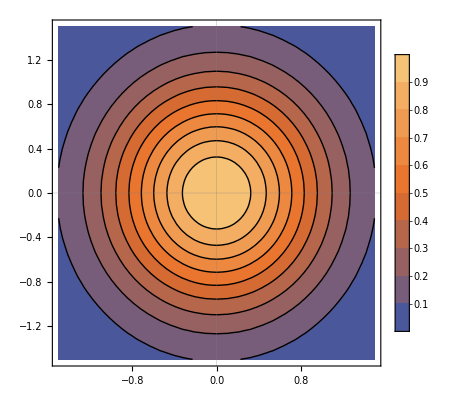

```mathematica
ContourPlot[initEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-xlim,xlim}, PlotLegends->Automatic, PlotTheme->"Scientific"]
```

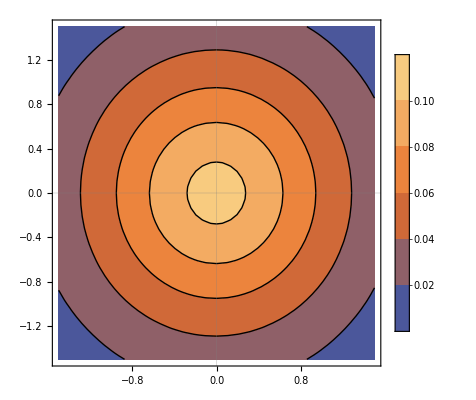

```mathematica
ContourPlot[streamedEnergyDensityInterp[x,y, 0],{x,-xlim, xlim},{y,-xlim,xlim}, PlotLegends->Automatic, PlotTheme->"Scientific"]
```